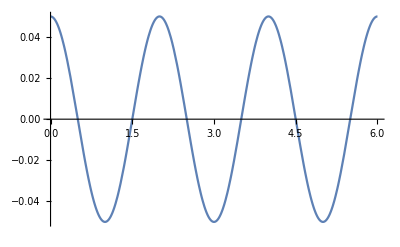

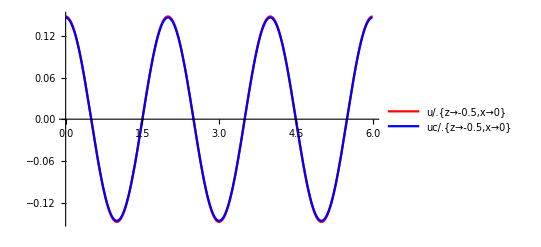

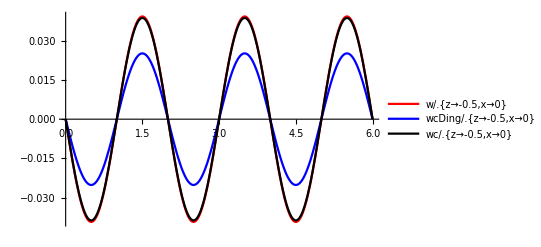

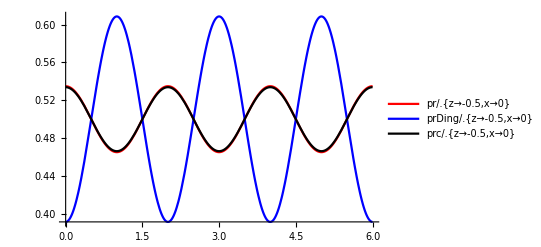

-Graphics-

```mathematica
ClearAll["Global`*"]
H=0.1;
T=2;
d=0.7;
L=4.623646;
w=2*Pi/T;
k=2*Pi/L;
pha=k*x-w*t;

eta=H/2*Cos[pha];
u=Pi*H/T*Cosh[k*(d+z)]/Sinh[k*d]*Cos[pha];
w=Pi*H/T*Sinh[k*(d+z)]/Sinh[k*d]*Sin[pha];
pr=Cosh[k*(d+z)]/Cosh[k*d]*eta - z;

um=Integrate[u,{z,-d,0}]/(d);
umx=D[um,x];
umxx=D[umx,x];
umxxx=D[umxx,x];
umxt=D[umx,t];

uc = um +umxx*(- 0.5*d*d + d*d/6 - z*d - 0.5*z*z);
wcDing = -d*umx -z*umx +umxxx*(- d*d*d/2 + d*d*d/6 +z*z*d/2 + z*z*z/6);
wc = -d*umx -z*umx +umxxx*(z*d*d/2 -z*d*d/6 +z*z*d/2 + z*z*z/6);
prDing=-z+eta+(z*d+z*z/2)*( umxt );
prc=-z+eta+(z*d+z*z/2)*( umxt )/9.81;

Plot[eta/.{z->-0.5,x->0},{t,0,6}]
Plot[{u/.{z->-0.5,x->0},uc/.{z->-0.5,x->0}},{t,0,6},PlotStyle->{Red,Blue,Black},PlotLegends->"Expressions"]
Plot[{w/.{z->-0.5,x->0},wcDing/.{z->-0.5,x->0},wc/.{z->-0.5,x->0}},{t,0,6},PlotStyle->{Red,Blue,Black},PlotLegends->"Expressions"]
Plot[{pr/.{z->-0.5,x->0},prDing/.{z->-0.5,x->0},prc/.{z->-0.5,x->0}},{t,0,6},PlotStyle->{Red,Blue,Black},PlotLegends->"Expressions"]
```